```mathematica
U={{1.23370055},{0.74460415,1.05302929,0.74460415},{0.38763947,0.71626434,0.93584446,1.01295075,0.93584446,0.71626434,0.38763947},{0.19571831,0.38391528,0.55735859,0.70938293,0.83414608,0.92685347,0.98394239,1.00321896,0.98394239,0.92685347,0.83414608,0.70938293,0.55735859,0.38391528,0.19571831}}
```

{{1.2337},{0.744604,1.05303,0.744604},{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639},{0.195718,0.383915,0.557359,0.709383,0.834146,0.926853,0.983942,1.00322,0.983942,0.926853,0.834146,0.709383,0.557359,0.383915,0.195718}}

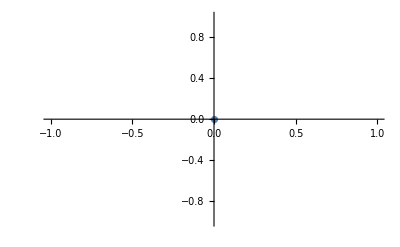

```mathematica
ListPlot[Insert[U[[1]],{0,0},2],PlotRange->Automatic]
```

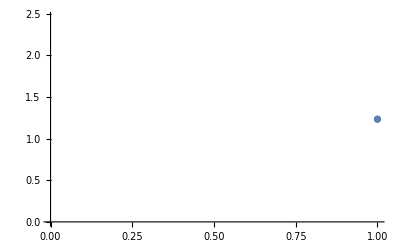

```mathematica
ListPlot[[Insert[,{0,0},1],PlotRange->Automatic]
```

```mathematica
Insert[U[[1]],{0,0},1]
```

```mathematica
{{0,0},1.23370055}
n=2
```

{{0,0},1.2337}

2

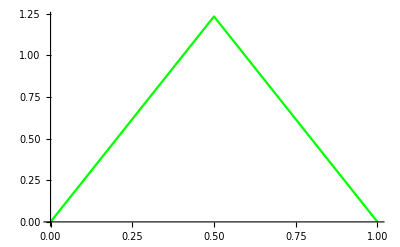

```mathematica
G1=ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->Green]
```

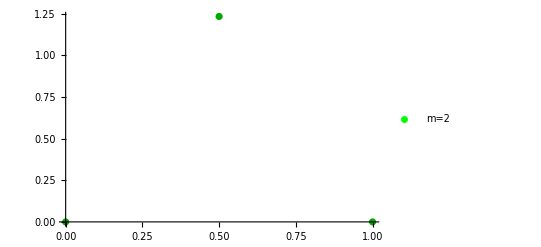

```mathematica
G2=ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->Darker[Green],PlotLegends->(Placed[#,Right]&/@{PointLegend[{Green},{"m=2"}]})]
```

```mathematica
n=4
```

4

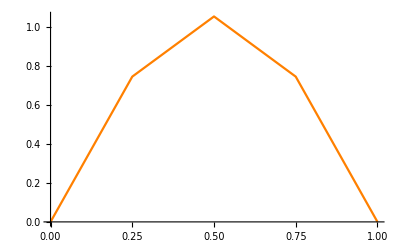

```mathematica
G3=ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->Orange]
```

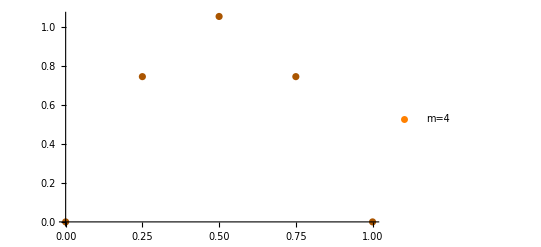

```mathematica
G4=ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->Darker[Orange],PlotLegends->(Placed[#,Right]&/@{PointLegend[{Orange},{"m=4"}]})]
```

```mathematica
n=8
```

8

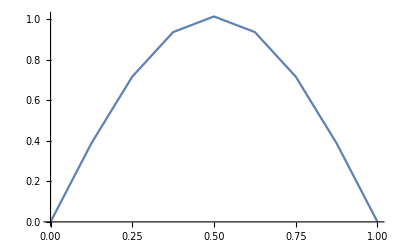

```mathematica
G5=ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True]
```

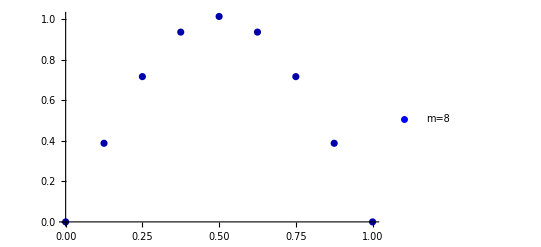

```mathematica
G6=ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->Darker[Blue],PlotLegends->(Placed[#,Right]&/@{PointLegend[{Blue},{"m=8"}]})]
```

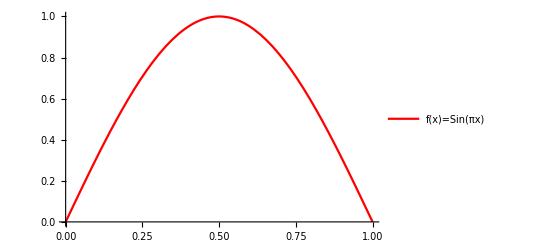

```mathematica
H2=Plot[Sin[Pi*x],{x,0,1},PlotStyle->Red,PlotLegends->(Placed[#,Right]&/@{LineLegend[{Red},{"f(x)=Sin(πx)"}]})]
```

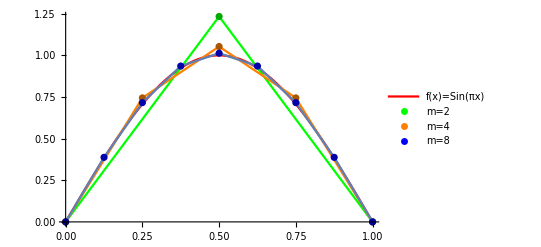

```mathematica
plot=Show[H2,G1,G2,G3,G4,G5,G6,PlotRange->Automatic]
```

```mathematica
fff-Graphics-
```

```mathematica
Rasterize[%510,"Image"]
```

-Graphics-

```mathematica
Rasterize[%510,"Image"]
```

-Graphics-

```mathematica
Export[gfxname<>".png",plot];

StringReplace["\\begin{figure}[!htb]\\centering
 \\includegraphics[width=1\\textwidth]{XXX}
 \\caption{Put your caption here.} 
 \\label{fig:XXX}
 \\end{figure}
 ","XXX"->gfxname]
```

StringJoin::string: String expected at position 1 in gfxname<>.png.

Export::chtype: First argument gfxname<>.png is not a valid file specification.

\begin{figure}[!htb]\centering
 \includegraphics[width=1\textwidth]{~~gfxname~~}
 \caption{Put your caption here.} 
 \label{fig:~~gfxname~~}
 \end{figure}

```mathematica
Show[H2,G1,G2,G3,G4,G5,G6,PlotRange->Automatic]
```

-Graphics-

```mathematica
I
```

```mathematica
G7=Framed[Column[{PointLegend[{ColorData[97,2^2-1],ColorData[97,4^2-1],ColorData[97,8^2-1],ColorData[97,16^2-1]},{"2","4","8","16"}],LineLegend[{ColorData[97,1^2-1]},{"f(x)=Sin(πx)"}]}],RoundingRadius->5]
```

```mathematica
Export["legends.pdf",G7]
```

legends.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["legends.pdf"]]]
```